# Naman Taggar

## Day 2 @ Numerical Optimisation Workshop

## 1. Bisection Method

```mathematica
bisectionMethod[func_, var_, l_List, n_: 10, eps_: 0.0000005]:=Module[
{xmin, xmax, f, fv, mid},
Catch[
xmin = l[[1]]; xmax = l[[2]];
f[fv_]:= func/.var->fv;
For[i = 1, i <= n, i++,
mid = (xmin + xmax)/2;
If[f[mid] == 0, Throw[{i, N[mid, 10], N[f[mid], 10]}],
If[f[xmin]f[mid]<0, xmax = mid, xmin = mid]
]
];
Throw[{n,N[mid, 10], N[f[mid], 10]}]
]
]
```

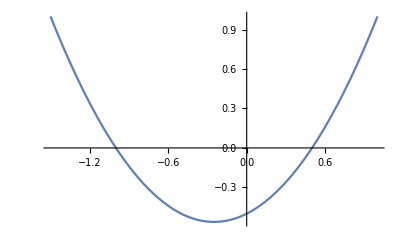

{10,0.500098,0.000146494}

```mathematica
f[x_]:=(x-0.5)(x+1);
Plot[f[x], {x, -1.5, 1}]
bisectionMethod[f[x], x, {0.3, 0.6}, 10]
```

So, at the tenth iteration, x = 0.500098 and f(x) = 0.000146494.

## 2. Gradient Descent Method

```mathematica
gDMethod[func_, var_, init_, iterations_: 10,learningRate_:0.1]:=Module[
{f, ivar, grad,new, old},
Catch[
old = init;
f[ivar_]:=func/.var->ivar;
grad[ivar_]:=f'[ivar];
For[i = 1, i<= iterations, i++,
new = old - learningRate*grad[old];
old = new
];
Throw[{iterations, new, f[new]}]
]
]
```

```mathematica
gDMethod[x^2-6x+9, x, 2]
```

{10,2.89263,0.0115292}

## 3. Newton Method

```mathematica
newtonMethod[expr_, var_, l_List, n_: 10, eps_: 0.0000005]:=Module[
{f, fv, xc,  init, deriv},
Catch[
init = (l[[1]]+ l[[2]])/2;
f[fv_] := expr/.var->fv;
deriv = f'[var];
For[i =1, i <= n, i++,
xc = init-f[init]/(deriv/.var->init);
If[Abs[f[xc]]<= eps, Throw[{i, N[xc, 10], N[f[xc], 10]}]];
init = xc
];
Throw[{n, N[xc, 10], N[f[xc], 10]}]
]
]
```

```mathematica
newtonMethod[Cos[x] - x Exp[x], x, {0, 1}, 20]
```

{2,0.5177574241,-1.83784191×10^-7}

## 4. Secant Method

```mathematica
secantMethod[expr_, var_, l_List, n_: 10, eps_: 0.0000005]:=Module[
{f, fv, init, p1, p2},
{p1, p2} = {l[[1]], l[[2]]};
Catch[
init = (p1 + p2)/2;
f[fv_] := expr/.var->fv;
For[i =1, i <= n, i++,
p2 = p1 - f[p1](p1 - init)/(f[p1]-f[init]);
If[Abs[f[p2]]<= eps, Throw[{i, N[p2, 10], N[f[p2], 10]}]];
{init, p1} = {p1, p2};
];
Throw[{n, N[p2, 10], N[f[p2], 10]}]
]
]
```

```mathematica
secantMethod[x^3+2x^2-3x-1, x, {1, 2}]
```

{5,1.198691246,1.660120746×10^-8}

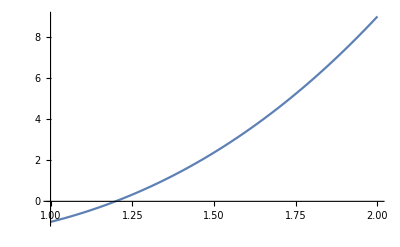

```mathematica
Plot[x^3+2x^2-3x-1, {x, 1, 2}]
```

## Perfect!

## 5. Gauss-Jacobi Method

```mathematica
(*My code*)
```

```mathematica
gsMat1= {{8,3,4,15},{-2,5,-2,1}, {1,1,3,5}}; (*Augmented matrix*)
```

```mathematica
gJMethod[A_List, maxiters_:10]:=Module[
{n, tuple},
n = Dimensions[A][[1]];
Catch[
If[Dimensions[A][[1]]+1 == Dimensions[A][[2]], Nothing[], Throw["Invalid matrix supplied."]];
tuple = Table[0, {i,n}];
For[i = 1, i<= maxiters, i++,
For[ni=1, ni<= n, ni++, 
tuple[[ni]] = N[1/A[[ni]][[ni]] (A[[ni, n + 1]] - Sum[A[[ni, r]]tuple[[r]], {r, Complement[Table[1, n], {ni}]}]), 10];
];
];
Throw[{i - 1, tuple}]
]
]
```

```mathematica
gJMethod[gsMat1]
```

{10,{1.875,0.95,1.041666667}}

## 6. Gauss-Seidal Method

```mathematica
(*Sir's Code*)
```

```mathematica
gSMethod[a0_,b0_,x0_,e0_,m0_]:=Module[{},A=a0;
B=b0;
X=x0;
n=Length[X];
e=N[e0];
m=N[m0];
k=0;
X1=X;
While[k<m,For[i=1,i≤n,i++,X1[[i]]=N[(1/A[[i,i]])*(B[[i]]-Sum[A[[i,j]]*X1[[j]],{j,1,i-1}]-Sum[A[[i,j]]*X[[j]],{j,i+1,n}])];];
If[Norm[X1-X]<e,Break[]];
X=X1;];k++ ;
Print[NumberForm[X1,10]]]
A={{5,1,2},{-3,9,4},{1,2,-7}};
B={10,-14,-33};
X={0,0,0};
gSMethod[A,B,X,10^(-5),25]
```

{0.9999989607,-3.000000895,3.999999596}

## SOR Method

```mathematica
(*Sir's Code*)
```

```mathematica
sORMethod[a0_,b0_,x0_,w0_,e0_,m0_]:=Module[{},A=a0;
B=b0;
X=x0;
w=N[w0];
e=N[e0];
m=N[m0];
n=Length[X];
k=0;
X1=X;
While[k<m,For[i=1,i≤n,i++,X1[[i]]=N[(1-w)*X[[i]]+w*(1/A[[i,i]])*(B[[i]]-Sum[A[[i,j]]*X1[[j]],{j,1,i-1}]-Sum[A[[i,j]]*X[[j]],{j,i+1,n}])];];
If[Norm[X1-X]<e,Break[]];
X=X1;];k++ ;
Print[NumberForm[X1,10]];]
A={{5,1,2},{-3,9,4},{1,2,-7}};
B={10,-14,-33};
X={0,0,0};
sORMethod[A,B,X,0.9,10^(-5),25]
```

{0.9999992301,-2.999999652,3.99999992}

End of file namantaggar_NAWorkshop_day2practical.pdf